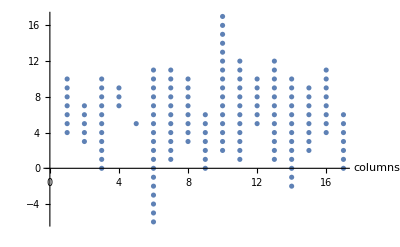

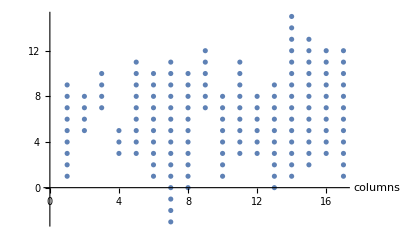

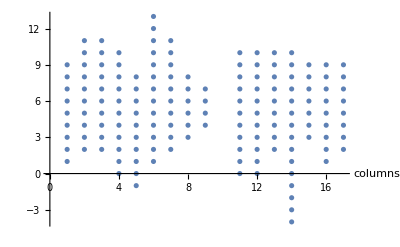

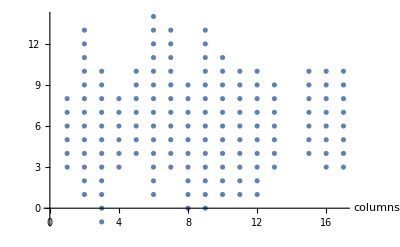

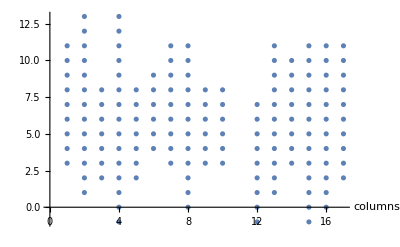

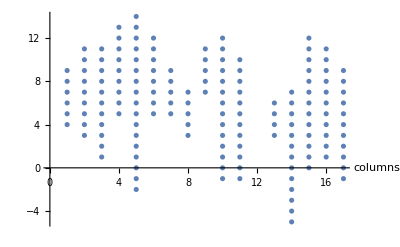

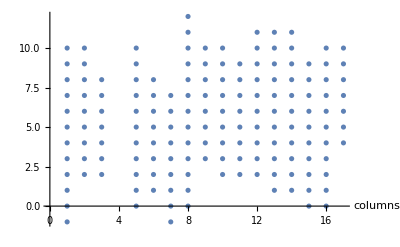

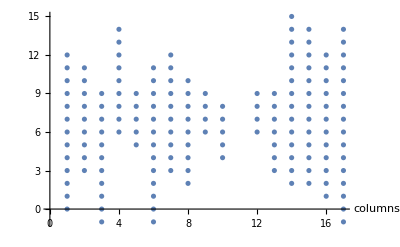

```mathematica
Do[top=ReadList[TemplateApply["C:\\Users\\刘兴瑞\\Documents\\Visual Studio 2015\\Projects\\pillars\\pillars\\top``.txt",{i}],Number];
bottom=ReadList[TemplateApply["C:\\Users\\刘兴瑞\\Documents\\Visual Studio 2015\\Projects\\pillars\\pillars\\bottom``.txt",{i}],Number];
pillar={};
Do[Do[pillar=Append[pillar,{i,top[[i]]-j+1}],{j,1,top[[i]]-bottom[[i]]-1}],{i,1,Length[top]}]
Print[ListPlot[pillar,AxesLabel->{"columns",""}]],{i,1,10}]
```

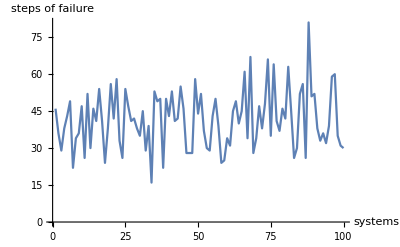

```mathematica
failTime=ReadList["C:\\Users\\刘兴瑞\\Documents\\Visual Studio 2015\\Projects\\pillars\\pillars\\fail_time.txt",Number];
ListLinePlot[failTime,AxesLabel->{"systems","steps of failure"}]
```

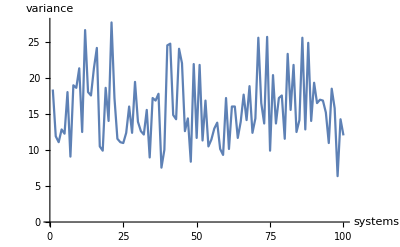

```mathematica
variance=ReadList["C:\\Users\\刘兴瑞\\Documents\\Visual Studio 2015\\Projects\\pillars\\pillars\\variance.txt",Number];
ListLinePlot[variance,AxesLabel->{"systems","variance"}]
```

```mathematica
failTime
```

{46,36,29,38,43,49,22,34,36,47,26,52,30,46,41,54,41,24,38,56,42,58,33,26,54,47,41,42,38,35,45,29,39,16,53,49,50,22,50,43,53,41,42,55,46,28,28,28,58,44,52,37,30,29,43,50,39,24,25,34,31,45,49,40,45,61,34,67,28,34,47,38,48,66,35,64,41,37,46,42,63,45,26,30,52,56,26,81,51,52,38,33,36,32,39,59,60,35,31,30}

```mathematica
variance
```

{18.3529,11.8824,11.0588,12.8235,12.2353,18,9.05882,18.9412,18.5882,21.2941,12.4706,26.5882,18,17.5294,21.2941,24.1176,10.4706,9.88235,18.5882,14,27.6471,17.1765,11.5294,11.0588,10.9412,12.3529,16,12.3529,19.4118,13.8824,12.5882,12.1176,15.5294,8.94118,17.1765,16.8235,17.7647,7.52941,10,24.4706,24.7059,14.8235,14.2353,24,22,12.5882,14.3529,8.35294,21.8824,11.6471,21.7647,11.2941,16.8235,10.4706,11.4118,12.9412,13.7647,10.1176,9.29412,17.1765,10.1176,16,16,11.6471,13.8824,17.6471,14.1176,18.8235,12.3529,14.3529,25.5294,16.4706,13.6471,25.6471,9.88235,20.3529,13.6471,17.1765,17.5294,11.5294,23.2941,15.5294,21.7647,12.4706,14.1176,25.5294,12.8235,24.8235,14,19.2941,16.4706,16.9412,16.8235,15.1765,10.9412,18.4706,15.7647,6.35294,14.2353,12}